## Data visualization pre and post by WOS

### Sorting parameters pre and postValues

```mathematica
preValues=({{α->0.1400, Dv->1125}, {α->0.6400, Dv->525}, {α->0.4800, Dv->125}, {α->0.0700, Dv->125}, {α->0.1100, Dv->1225}, {α->0.1200, Dv->725}, {α->0.0600, Dv->825}, {α->0.1900, Dv->1025}, {α->0.0800, Dv->825}, {α->0.0900, Dv->725}, {α->0.0800, Dv->825}, {α->0.1800, Dv->225}, {α->0.1000, Dv->225}, {α->0.0900, Dv->125}, {α->0.2500, Dv->225}, {α->0.5200, Dv->1925}, {α->0.0500, Dv->1025}, {α->0.0300, Dv->425}, {α->0.0300, Dv->125}, {α->0.1200, Dv->25}});
αPre=Table[α/.preValues[[i,1]],{i,1,20}];
μPre=Table[0,{i,1,20}];
DvPre=Table[Dv/.preValues[[i,2]],{i,1,20}];

postValues=({{α->0.0100, μ->0.0004, Dv->225}, {α->0.3400, μ->0.0136, Dv->425}, {α->0.0100, μ->0, Dv->125}, {α->0.0400, μ->0.0016, Dv->125}, {α->0.0200, μ->0.0008, Dv->225}, {α->0.0600, μ->0.0024, Dv->525}, {α->0.1100, μ->0, Dv->125}, {α->0.1800, μ->0, Dv->625}, {α->0.2900, μ->0.0116, Dv->25}, {α->0.1200, μ->0, Dv->1125}, {α->0.0200, μ->0.0008, Dv->25}, {α->0.2700, μ->0.0108, Dv->225}, {α->0.0300, μ->0, Dv->25}, {α->0.1000, μ->0, Dv->125}, {α->0.1500, μ->0, Dv->625}, {α->0.2000, μ->0.0080, Dv->1925}, {α->0.0400, μ->0, Dv->325}, {α->0.1400, μ->0.0056, Dv->1525}, {α->0.0300, μ->0, Dv->125}, {α->0.2000, μ->0.0080, Dv->25}});

αPost=Table[α/.postValues[[i,1]],{i,1,20}];
μPost=Table[μ/.postValues[[i,2]],{i,1,20}];
DvPost=Table[Dv/.postValues[[i,3]],{i,1,20}];
```

```mathematica
Export["mu.txt",μPost-μPre]
Export["alpha.txt",αPost-αPre]
Export["Dv.txt",DvPost-DvPre]
Export["alphamu.txt",αPost-μPost-(αPre-μPre)]
```

mu.txt

alpha.txt

Dv.txt

alphamu.txt

### α

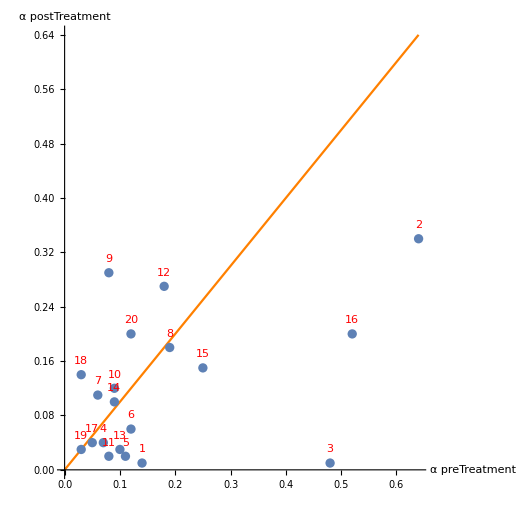

```mathematica
patientID=Range[1,20]; (*For labeling data points*)
αPrePostData=Transpose@{αPre,αPost,patientID}; 
labels=Text[#[[3]],{#[[1]],0.02+#[[2]]}]&/@αPrePostData;
Show[
Plot[α,{α,0,Max[αPre]},
PlotStyle->Orange,
PlotRange->All,
AspectRatio->1,
AxesLabel->{"α preTreatment","α postTreatment"}
],
ListPlot[αPrePostData[[All,{1,2}]]],
Graphics[{Red,labels}]
]
```

### μ

ListPlot

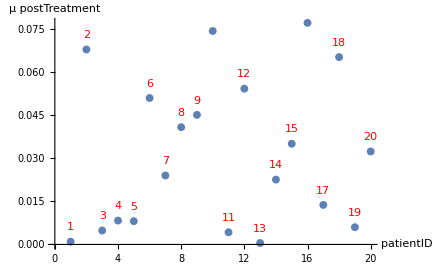

```mathematica
ListPlot
patientID=Range[1,20]; (*For labeling data points*)
μPrePostData=Transpose@{μPre,μPost,patientID}; 
labels=Text[#[[3]],{#[[3]],0.005+#[[2]]}]&/@μPrePostData;
Show[
ListPlot[μPost],
Graphics[{Red,labels}],
AxesLabel->{"patientID","μ postTreatment"}
]
```

### Dv

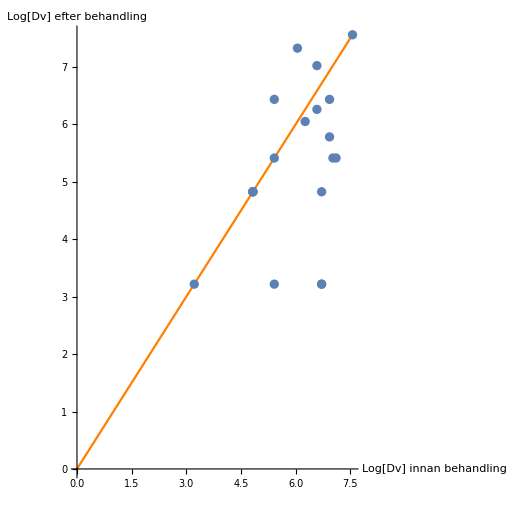

```mathematica
patientID=Range[1,20]; (*For labeling data points*)
DvPrePostData=Transpose@{Log[DvPre],Log[DvPost],patientID}; 
labels=Text[#[[3]],{#[[1]],0.1+#[[2]]}]&/@DvPrePostData;
Show[
Plot[Dv,{Dv,0,Max[Log[DvPre]]},
PlotStyle->Orange,
PlotRange->All,
AspectRatio->1,
AxesLabel->{"Log[Dv] innan behandling","Log[Dv] efter behandling"}
],
ListPlot[DvPrePostData[[All,{1,2}]]]
(*Graphics[{Red,labels}]*)
]
```

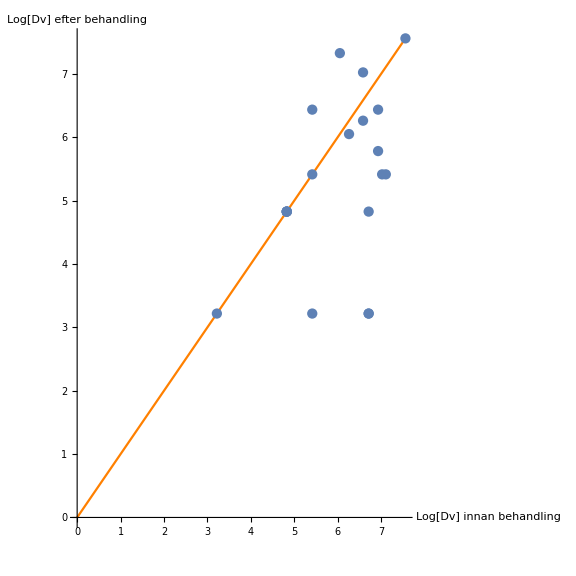

```mathematica
Show[%22,ImageSize->Large]
```

```mathematica
Export["/Users/HAL/Desktop/KandidatPDE/changeDvNum.jpg",%27,"JPEG"]
```

/Users/HAL/Desktop/KandidatPDE/changeDvNum.jpg

```mathematica
Export["/Users/HAL/Desktop/KandidatPDE/DvRelative.jpg",%22,"JPEG"]
```

/Users/HAL/Desktop/KandidatPDE/DvRelative.jpg

### α-μ

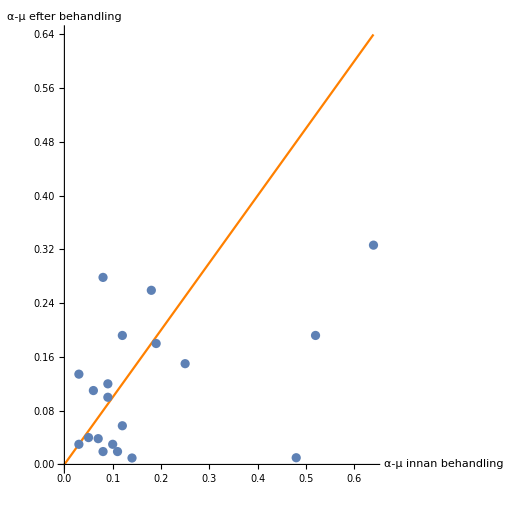

```mathematica
αμPre=αPre-μPre;
αμPost=αPost-μPost;
patientID=Range[1,20]; (*For labeling data points*)
αμPrePostData=Transpose@{αμPre,αμPost,patientID}; 
labels=Text[#[[3]],{#[[1]],0.02+#[[2]]}]&/@αμPrePostData;
Show[
Plot[αμ,{αμ,0,Max[αμPre]},
PlotStyle->Orange,
PlotRange->All,
AspectRatio->1,
AxesLabel->{"α-μ innan behandling","α-μ efter behandling"}
],
ListPlot[αμPrePostData[[All,{1,2}]]]
(*Graphics[{Red,labels}]*)
]
```

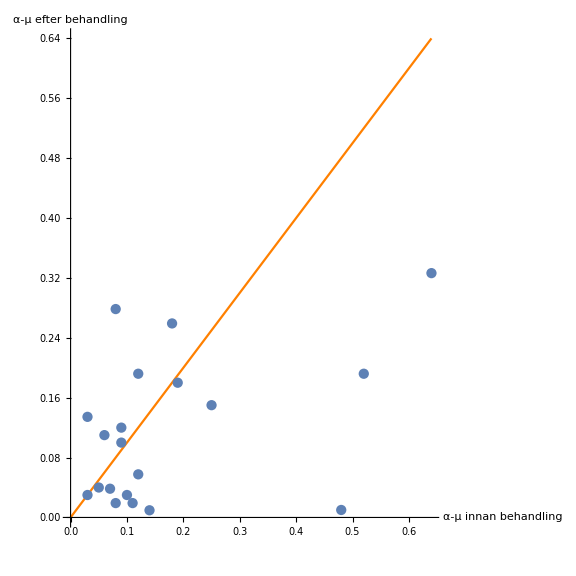

```mathematica
Show[%18,ImageSize->Large]
```

```mathematica
Export["/Users/HAL/Desktop/KandidatPDE/changeAlphaNum.jpg",%25,"JPEG"]
```

/Users/HAL/Desktop/KandidatPDE/changeAlphaNum.jpg

```mathematica
Export["/Users/HAL/Desktop/KandidatPDE/AlphaMuRelative.jpg",%18,"JPEG"]
```

/Users/HAL/Desktop/KandidatPDE/AlphaMuRelative.jpg